```mathematica
allGraphs5[alfa1Key,"colofour"]/.RepGraph["C"]
```

-Graphics-361660

```mathematica
Bases//Keys
```

{C,E,G,F,T}

```mathematica
Table[   BaseFormula[alfa1Key,b]/.RepGraph[b],{b,Keys[Bases]}]//TableForm
```

-Graphics-361660
2 -Graphics-590481--Graphics-575282--Graphics-147481--Graphics-133401+-Graphics-132842
-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240
1/12 (-2 -Graphics-1968321+4 -Graphics-656124-2 -Graphics-218724-2 -Graphics-24321+4 -Graphics-8124-2 -Graphics-921+2 -Graphics-1968615+2 -Graphics-1968413-4 -Graphics-658816-4 -Graphics-656215+2 -Graphics-221416+2 -Graphics-219016+2 -Graphics-97213-4 -Graphics-81015+2 -Graphics-73813+2 -Graphics-24413-4 -Graphics-8416+2 -Graphics-3615+2 -Graphics-204398-4 -Graphics-72939+2 -Graphics-29178+2 -Graphics-2739-4 -Graphics-1099+2 -Graphics-138--Graphics-264885--Graphics-219545--Graphics-204485--Graphics-196965--Graphics-87845+5 -Graphics-73745+5 -Graphics-66705--Graphics-31605--Graphics-24605--Graphics-10625+-Graphics-287640--Graphics-272460--Graphics-227080--Graphics-94900--Graphics-3640+-Graphics-295240)
--Graphics-368980+-Graphics-354340

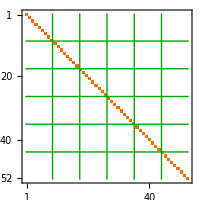
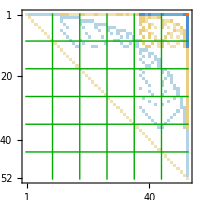
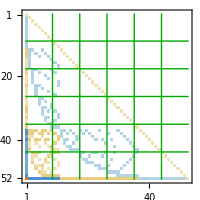
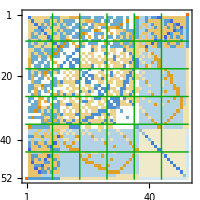
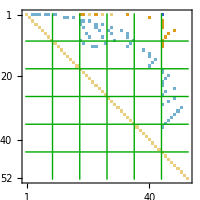
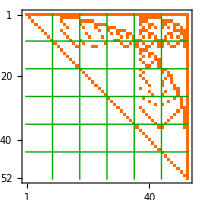
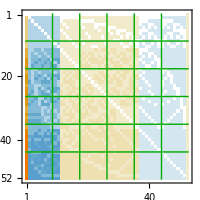
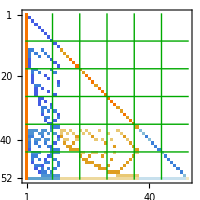
| C | E | G | F | T
C | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix[b1,b2],Mesh->5,MeshStyle->Darker[Green],ImageSize->200],{b1,Keys[Bases]},{b2,Keys[Bases]}],TableHeadings->{Keys[Bases],Keys[Bases]}, TableAlignments->Center]
```

```mathematica
GraphFormula[k_,b_:"C"]:=BaseFormula[k,b]/.RepGraph[b]
```

```mathematica
GraphFormula[10,"G"]
```

-Graphics-22788+-Graphics-270643+-Graphics-221503+-Graphics-75703--Graphics-292511--Graphics-222311--Graphics-294400--Graphics-273340--Graphics-98381+2 -Graphics-295210